## Importing data

```mathematica
Vds = {0.0031547183613752743,0.06954096561814191,0.12783467446964156,0.17529261155815654,0.24250182882223847,0.30875091441111924,0.3728054133138259,0.4453639356254572,0.5260149963423555,0.5876005852231163,0.6548098024871982,0.7122805413313825,0.7973207754206291,0.8790691294806144,0.9488844184345281,1.0321415508412581,1.112381126554499,1.1971470373079736,1.2828730797366494,1.3699707388441842,1.4629663496708118,1.5491038771031456,1.644705559619605,1.7289228237015362,1.832205559619605,1.9180687637161666,2.0304041697147035,2.140956474030724,2.2530175566934894,2.3525969275786394,2.4667154352596925,2.5783650329188,2.7181327724945135,2.848573518653987,2.996159473299195,3.1512893196781273,3.323838697878566,3.4658010241404535,3.668937454279444,3.865078639356254,4.067666422823701,4.300018288222384,4.552532918800292,4.811905632772494,5.063185808339429,5.352459765910753,5.646534381858083,5.961046086320409,6.271031455742501,6.595830285296269,6.884281272860278,7.170674835405998,7.4646122896854425,7.783787490855889,8.126143013899048,8.456016825164594,8.793297366495976,9.120702267739576,9.493782004389173,9.810625457205559,10.169166057059254,10.46735552304316,10.77240307242136,11.051389904901242,11.319678127286027,11.597156181419166,11.917291514264813,0.03305596196049744,0.0718727139722019,0.13153803950256035,0.22988295537673736,0.28927395757132407,0.34935076810534016,0.41011338697878563,0.49282187271397215,0.5615398683247989,0.6408193123628383,0.6822421360643744,0.7383412582297,0.8167977322604243,0.9084217264081931,0.9720647403072421,1.053127286027798,1.1044257498171177,1.1907004389173372,1.2990581565471835,1.36078090709583,1.429498902706657,1.5220830285296267,1.6024597659107533,1.6936722750548645,1.7981894659839062,1.9109363569861009,2.0020117044623262,2.1264173372348205,2.257818215069495,2.353831382589612,2.498948427212875,2.6383046817849305,2.7617501828822237,2.897814557425018,3.049515362106803,3.225493782004389,3.362106803218727,3.538222384784199,3.7286027798098025,3.9357168983174833,4.127743233357718,4.356391733723481,4.569678127286028,4.7851591075347475,4.99789685442575,5.233129114850036,5.464109363569861,5.67328090709583,5.900969275786394,6.12289685442575,6.359912216532552,6.596927578639356,6.849305047549378,7.103054133138259,7.3433613752743225,7.637161667885881,7.944678127286028,8.227779809802486,8.548326627651791,8.846516093635698,9.143608266276518,9.48390636430139,9.769888441843452,10.044897585954645,10.334171543525969,10.638944769568397,10.909016093635698,11.184436722750547,11.459034381858082,11.721836137527431,12.015499268471103,0.019065471836137528,0.11946781272860277,0.1887344550109729,0.30052121433796636,0.3837783467446964,0.46182333577176293,0.5619513533284565,0.6535753474762253,0.7489027066569129,0.8535570592538405,0.9553310168251645,1.0764447695683979,1.2018105340160936,1.3373262618873445,1.4843635698610094,1.637710314557425,1.8023043160204828,1.9590801024140452,2.137801755669349,2.3534198975859546,2.5709583028529623,2.791788588149232,3.0039776883686904,3.222201901975128,3.448518653986832,3.666194220921726,3.9081474030724213,4.151060716898317,4.413999634235552,4.675292611558156,4.943032187271397,5.219412948061448,5.464932333577176,5.757361009509875,6.046360643745428,6.331519751280175,6.647677395757132,6.951216166788588,7.2317117776152156,7.543205925384052,7.836320409656181,8.157004389173371,8.483860643745427,8.790279809802486,9.153072421360644,9.446735552304315,9.737929773226043,10.037216532553035,10.341303950256034,10.622759692757864,10.894476956839794,11.188140087783466,11.462874908558888,11.734592172640818,11.979837234820774,0.050338332114118506,0.12358266276517922,0.19353511338697876,0.2932516459400146,0.39379114850036573,0.5192940746159473,0.6500091441111924,0.7956748354059985,0.9498445501097292,1.0949615947329918,1.2768379663496707,1.4573427212874908,1.6565014630577908,1.8674561082662764,2.0882863935625458,2.3152889539136794,2.5398226042428673,2.7884967081199705,3.0463606437454276,3.311219824433065,3.5745702267739574,3.8466989758595465,4.123491221653255,4.361329553767374,4.617684711046086,4.88130943672275,5.118324798829553,5.40019202633504,5.639676298463789,5.85378566203365,6.085863204096562,6.358952084857352,6.60776335040234,6.852596927578639,7.113478419897586,7.37312545720556,7.649506217995611,7.899551938551572,8.136155815654718,8.379754937820044,8.643791148500366,8.881355157278712,9.132635332845647,9.384464155084125,9.63039502560351,9.868507681053401,10.123079736649597,10.368873445501096,10.620016459400146,10.866495976591075,11.123125457205559,11.365764447695684,11.609226408193123,11.863249817117776,-0.02606071689831748,0.1333211411850768,0.3267190929041697,0.556739209948793,0.8150146305779078,1.0690380395025603,1.3374634235552303,1.602871250914411,1.8612838332114117,2.117638990490124,2.378383321141185,2.671497805413314,2.930596196049744,3.189420263350402,3.4509875640087784,3.7205102414045355,3.9964795171909286,4.251463057790782,4.503840526700804,4.742090343818581,4.987198244330651,5.238615581565472,5.488249817117776,5.723482077542062,5.955833942940746,6.198061448427213,6.440014630577908,6.6912948061448425,6.935854059985369,7.174789685442574,7.433065106071689,7.676115581565472,7.94659839063643,8.184436722750549,8.447787125091441,8.687682882223847,8.931693489392831,9.206976956839794,9.47691111923921,9.713240673006583,9.955193855157278,10.205102414045355,10.462417702999268,10.749222750548647,11.068260790051207,11.343269934162398,11.595784564740306,11.896580102414045};
```

```mathematica
Ids = {-0.025331724969843185,2.086248492159228,4.420386007237636,6.627864897466828,8.810012062726177,11.130579010856453,13.329010856453559,15.365500603136308,17.9167671893848,20.169481302774425,22.498190591073584,24.580820265379977,26.891435464414958,29.197527141133897,31.233112183353438,33.50934861278649,36.02804583835947,38.07086851628468,40.482810615199035,42.647768395657415,44.92852834740651,46.917068757539205,48.968938480096504,51.136610373944514,53.22104945717732,55.21501809408927,57.449638118214715,59.32780458383595,61.28739445114596,63.39445114595899,65.26176115802171,67.2910132689988,69.24698431845597,71.23823884197829,73.33534378769602,75.22889022919179,77.1568154402895,78.97346200241255,80.77382388419782,82.54433051869722,84.37726176115802,86.09167671893847,87.86218335343787,89.34680337756333,90.84499396863691,92.15229191797346,93.30850422195417,94.55880579010856,95.67249698431846,96.63238841978287,97.4900482509047,98.27985524728588,99.0732810615199,99.93184559710494,100.71351025331725,101.55579010856454,102.24155609167671,103.00512665862485,103.73793727382389,104.33775633293124,105.02352231604343,105.68395657418577,106.11278648974668,106.61127864897466,107.1251507840772,107.58112183353438,108.125753920386,0.18727382388419783,1.8184559710494572,3.2406513872135103,5.4037997587454765,7.179734620024125,9.236127864897467,11.190289505428227,13.139927623642944,14.894149577804583,16.62213510253317,18.221652593486127,20.059107358262967,21.88841978287093,23.610977080820266,25.261158021712905,26.905910735826296,28.577804583835945,30.227985524728588,31.813027744270205,33.38449939686369,34.97587454764777,36.424306393244876,37.997587454764776,39.54825090470446,41.0934861278649,42.59439083232811,44.04644149577805,45.71562123039807,47.23552472858866,48.7192400482509,50.18214716525935,51.67129071170084,53.00844390832328,54.28045838359469,55.5624246079614,56.824487334137515,58.040410132689985,59.28709288299156,60.451447527141134,61.41224366706876,62.49336550060313,63.43697225572979,64.32539203860073,65.12243667068758,65.9583835946924,66.57810615199035,67.28648974668275,67.80307599517491,68.26537997587455,69.08685162846804,69.5301568154403,70.11188178528347,70.58685162846804,71.12243667068758,71.69240048250904,72.30850422195417,72.78890229191798,73.31905910735826,73.69179734620025,74.27623642943306,74.80367913148372,75.32931242460796,75.8648974668275,76.22135102533173,76.7388419782871,77.1767189384801,77.66254523522316,78.09047044632086,78.55910735826296,79.03588661037395,79.56966224366707,0.6242460796139928,2.6598311218335344,4.530759951749095,6.3347406513872135,8.13329312424608,9.580820265379975,11.300663449939686,13.205066344993968,14.89686369119421,16.67279855247286,18.35283474065139,20.123341375150783,21.83142340168878,23.472557297949336,25.2810615199035,27.04071170084439,28.688178528347407,30.303075995174908,31.697225572979495,33.20446320868516,34.69903498190591,35.95928829915561,36.966224366706875,37.80398069963812,38.6978287092883,39.54372738238842,40.2294933655006,40.84740651387214,41.55669481302775,42.05518697225573,42.63148371531966,43.132689987937276,43.58866103739445,44.09439083232811,44.584740651387214,45.10313630880579,45.45416164053076,45.91194209891435,46.325392038600725,46.86911942098914,47.17671893848009,47.63359469240048,47.9891435464415,48.448733413751505,48.79523522316043,49.208685162846805,49.642943305186975,49.89716525934861,50.185765983112184,50.60916767189385,50.9583835946924,51.3962605548854,51.82147165259349,52.207780458383596,52.43124246079614,-0.3410735826296743,1.1019300361881785,2.5738841978287095,3.9725572979493364,5.409227985524729,6.8124246079613995,8.15319662243667,9.622436670687575,11.02291917973462,12.194511459589867,13.419481302774427,14.534981905910735,15.630579010856453,16.61761158021713,17.534077201447527,18.2813630880579,18.84680337756333,19.379674306393245,19.951447527141134,20.337756332931242,20.73130277442702,21.15289505428227,21.476779252110976,21.88027744270205,22.10826296743064,22.324487334137515,22.61851628468034,22.929734620024124,23.192098914354645,23.430940892641736,23.594692400482508,23.90319662243667,24.032569360675513,24.154704463208684,24.33745476477684,24.610675512665864,24.799758745476478,25.070265379975876,25.311821471652593,25.522617611580216,25.7189384800965,25.946019300361883,26.145054282267793,26.239143546441497,26.496984318455972,26.665259348612786,26.91043425814234,27.02171290711701,27.237032569360675,27.47587454764777,27.857659831121833,28.084740651387214,28.34620024125452,28.721652593486127,-0.05971049457177322,0.7753317249698432,2.029252110977081,3.1248492159227985,3.896562123039807,4.608564535585042,5.143244873341375,5.531363088057901,5.982810615199035,6.123039806996381,6.305790108564535,6.439686369119421,6.667671893848009,6.7898069963811825,6.7898069963811825,6.99065138721351,7.056694813027744,7.181544028950543,7.2439686369119425,7.401387213510254,7.415862484921592,7.371531966224366,7.466525934861279,7.633896260554885,7.747889022919179,7.747889022919179,7.936972255729795,8.056393244873341,8.223763570566948,8.240952955367913,8.253618817852836,8.458986731001206,8.591978287092884,8.700542822677924,8.700542822677924,8.808202653799759,8.78015681544029,8.913148371531966,8.913148371531966,9.046139927623642,9.106755126658625,9.244270205066345,9.354644149577805,9.57177322074789,9.753618817852834,9.81151990349819,9.925512665862485,10.129071170084439}*(10^-6);
```

```mathematica
Vgs = {12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,12.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,10.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,8.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,6.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0,4.0};
```

## Models

```mathematica
data = Transpose[{Vds,Vgs,Ids}];
Vdseff[d_,g_,t_,a_]:= If[(g-t)/a>= d,d,(g-t)/a];
model =  α*gain*((vgs-vth)/α*Vdseff[vds,vgs,vth,α]-(Vdseff[vds,vgs,vth,α])^2/2)(1+λ*vds);
nlm = NonlinearModelFit[data,model,{α,gain,vth,λ},{vds,vgs}]
nlm["ParameterTable"]
```

FittedModel[…]

| Estimate | Standard Error | t-Statistic | P-Value
α | 2.56646 | 0.0409219 | 62.716 | 4.30639×10^-171
gain | 2.77606×10^-6 | 2.47735×10^-8 | 112.058 | 2.16711×10^-241
vth | 0.112946 | 0.0496725 | 2.27382 | 0.0237052
λ | 0.040586 | 0.00177847 | 22.8207 | 8.66967×10^-67

```mathematica
data1 = Transpose[{Vds,Vgs,Ids,Ids}];
Vdseff1[d_,i_,r_,g_,t_,a_]:= If[(g-t)/a>=d-2*i*r,d-2*i*r,(g-t)/a];
model1 = α*gain*((vgs-vth)/α*Vdseff1[vds,ids,R,vgs,vth,α]-(Vdseff1[vds,ids,R,vgs,vth,α])^2/2)+gain*(α-1)*(0.026)^2 E^((vgs-vth)/(0.026*α))(1-E^(-vds/0.026));
nlm1 = NonlinearModelFit[data1,model1,{α,gain,vth,λ,R},{vds,vgs,ids}]
nlm1["ParameterTable"]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[…]

General::munfl: -1. 6.11292096088182×10^-387 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.96509×10^-191 6.11292096088182×10^-387 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.63699×10^-198 6.11292096088182×10^-387 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
α | 1. | 0. | ∞ | 0.
gain | 1.45369×10^-6 | 0. | ∞ | 0.
vth | -0.0455907 | 0. | -∞ | 0.
λ | 1. | 0. | ∞ | 0.
R | -16896.3 | 0. | -∞ | 0.

```mathematica
data2 = Transpose[{Vds,Vgs,Ids}];
Vdseff2[d_,g_,t_,a_]:= If[(g-t)/a>=d,d,(g-t)/a];
model2 = α*gain*((vgs-vth)/α*Vdseff2[vds,vgs,vth,α]-(Vdseff2[vds,vgs,vth,α])^2/2)/(1-ld/(4*10^-6));
nlm2 = NonlinearModelFit[data2,{model2},{α,gain,vth,ld},{vds,vgs}]
nlm2["ParameterTable"]
```

FittedModel[…]

General::munfl: Exp[-789.788] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
α | 1.7541 | 0.0277155 | 63.2896 | 3.6458×10^-172
gain | -0.747245 | 0.00644068 | -116.02 | 1.09768×10^-245
vth | 0.401003 | 0.0806569 | 4.97171 | 1.13548×10^-6
ld | 1.10598 | 0.00435161 | 254.154 | 0.

## Another Fit

```mathematica
vds = {0.0031547183613752743,0.06954096561814191,0.12783467446964156,0.17529261155815654,0.24250182882223847,0.30875091441111924,0.3728054133138259,0.4453639356254572,0.5260149963423555,0.5876005852231163,0.6548098024871982,0.7122805413313825,0.7973207754206291,0.8790691294806144,0.9488844184345281,1.0321415508412581,1.112381126554499,1.1971470373079736,1.2828730797366494,1.3699707388441842,1.4629663496708118,1.5491038771031456,1.644705559619605,1.7289228237015362,1.832205559619605,1.9180687637161666,2.0304041697147035,2.140956474030724,2.2530175566934894,2.3525969275786394,2.4667154352596925,2.5783650329188,2.7181327724945135,2.848573518653987,2.996159473299195,3.1512893196781273,3.323838697878566,3.4658010241404535,3.668937454279444,3.865078639356254,4.067666422823701,4.300018288222384,0.03305596196049744,0.0718727139722019,0.13153803950256035,0.22988295537673736,0.28927395757132407,0.34935076810534016,0.41011338697878563,0.49282187271397215,0.5615398683247989,0.6408193123628383,0.6822421360643744,0.7383412582297,0.8167977322604243,0.9084217264081931,0.9720647403072421,1.053127286027798,1.1044257498171177,1.1907004389173372,1.2990581565471835,1.36078090709583,1.429498902706657,1.5220830285296267,1.6024597659107533,1.6936722750548645,1.7981894659839062,1.9109363569861009,2.0020117044623262,2.1264173372348205,2.257818215069495,2.353831382589612,2.498948427212875,2.6383046817849305,2.7617501828822237,2.897814557425018,3.049515362106803,3.225493782004389,3.362106803218727,0.019065471836137528,0.11946781272860277,0.1887344550109729,0.30052121433796636,0.3837783467446964,0.46182333577176293,0.5619513533284565,0.6535753474762253,0.7489027066569129,0.8535570592538405,0.9553310168251645,1.0764447695683979,1.2018105340160936,1.3373262618873445,1.4843635698610094,1.637710314557425,1.8023043160204828,1.9590801024140452,2.137801755669349,2.3534198975859546,0.050338332114118506,0.12358266276517922,0.19353511338697876,0.2932516459400146,0.39379114850036573,0.5192940746159473,0.6500091441111924,0.7956748354059985,0.9498445501097292,1.0949615947329918,1.2768379663496707,1.4573427212874908,-0.02606071689831748,0.1333211411850768,0.3267190929041697,0.556739209948793,0.8150146305779078,1.0690380395025603,1.3374634235552303};
ids = {-0.025331724969843185,2.086248492159228,4.420386007237636,6.627864897466828,8.810012062726177,11.130579010856453,13.329010856453559,15.365500603136308,17.9167671893848,20.169481302774425,22.498190591073584,24.580820265379977,26.891435464414958,29.197527141133897,31.233112183353438,33.50934861278649,36.02804583835947,38.07086851628468,40.482810615199035,42.647768395657415,44.92852834740651,46.917068757539205,48.968938480096504,51.136610373944514,53.22104945717732,55.21501809408927,57.449638118214715,59.32780458383595,61.28739445114596,63.39445114595899,65.26176115802171,67.2910132689988,69.24698431845597,71.23823884197829,73.33534378769602,75.22889022919179,77.1568154402895,78.97346200241255,80.77382388419782,82.54433051869722,84.37726176115802,86.09167671893847,0.18727382388419783,1.8184559710494572,3.2406513872135103,5.4037997587454765,7.179734620024125,9.236127864897467,11.190289505428227,13.139927623642944,14.894149577804583,16.62213510253317,18.221652593486127,20.059107358262967,21.88841978287093,23.610977080820266,25.261158021712905,26.905910735826296,28.577804583835945,30.227985524728588,31.813027744270205,33.38449939686369,34.97587454764777,36.424306393244876,37.997587454764776,39.54825090470446,41.0934861278649,42.59439083232811,44.04644149577805,45.71562123039807,47.23552472858866,48.7192400482509,50.18214716525935,51.67129071170084,53.00844390832328,54.28045838359469,55.5624246079614,56.824487334137515,58.040410132689985,0.6242460796139928,2.6598311218335344,4.530759951749095,6.3347406513872135,8.13329312424608,9.580820265379975,11.300663449939686,13.205066344993968,14.89686369119421,16.67279855247286,18.35283474065139,20.123341375150783,21.83142340168878,23.472557297949336,25.2810615199035,27.04071170084439,28.688178528347407,30.303075995174908,31.697225572979495,33.20446320868516,-0.3410735826296743,1.1019300361881785,2.5738841978287095,3.9725572979493364,5.409227985524729,6.8124246079613995,8.15319662243667,9.622436670687575,11.02291917973462,12.194511459589867,13.419481302774427,14.534981905910735,-0.05971049457177322,0.7753317249698432,2.029252110977081,3.1248492159227985,3.896562123039807,4.608564535585042,5.143244873341375};
vgs = {-0.025331724969843185,2.086248492159228,4.420386007237636,6.627864897466828,8.810012062726177,11.130579010856453,13.329010856453559,15.365500603136308,17.9167671893848,20.169481302774425,22.498190591073584,24.580820265379977,26.891435464414958,29.197527141133897,31.233112183353438,33.50934861278649,36.02804583835947,38.07086851628468,40.482810615199035,42.647768395657415,44.92852834740651,46.917068757539205,48.968938480096504,51.136610373944514,53.22104945717732,55.21501809408927,57.449638118214715,59.32780458383595,61.28739445114596,63.39445114595899,65.26176115802171,67.2910132689988,69.24698431845597,71.23823884197829,73.33534378769602,75.22889022919179,77.1568154402895,78.97346200241255,80.77382388419782,82.54433051869722,84.37726176115802,86.09167671893847,0.18727382388419783,1.8184559710494572,3.2406513872135103,5.4037997587454765,7.179734620024125,9.236127864897467,11.190289505428227,13.139927623642944,14.894149577804583,16.62213510253317,18.221652593486127,20.059107358262967,21.88841978287093,23.610977080820266,25.261158021712905,26.905910735826296,28.577804583835945,30.227985524728588,31.813027744270205,33.38449939686369,34.97587454764777,36.424306393244876,37.997587454764776,39.54825090470446,41.0934861278649,42.59439083232811,44.04644149577805,45.71562123039807,47.23552472858866,48.7192400482509,50.18214716525935,51.67129071170084,53.00844390832328,54.28045838359469,55.5624246079614,56.824487334137515,58.040410132689985,0.6242460796139928,2.6598311218335344,4.530759951749095,6.3347406513872135,8.13329312424608,9.580820265379975,11.300663449939686,13.205066344993968,14.89686369119421,16.67279855247286,18.35283474065139,20.123341375150783,21.83142340168878,23.472557297949336,25.2810615199035,27.04071170084439,28.688178528347407,30.303075995174908,31.697225572979495,33.20446320868516,-0.3410735826296743,1.1019300361881785,2.5738841978287095,3.9725572979493364,5.409227985524729,6.8124246079613995,8.15319662243667,9.622436670687575,11.02291917973462,12.194511459589867,13.419481302774427,14.534981905910735,-0.05971049457177322,0.7753317249698432,2.029252110977081,3.1248492159227985,3.896562123039807,4.608564535585042,5.143244873341375};
```

```mathematica
data = Transpose[{vds,vgs,ids,ids}];
vdseff[vd_,vg_,vt_,α_,id_,R_] := If[(vg-vt)/α>vd-2*id*R,vd-2*id*R,(vg-vt)/α];
id1 = α1*gain1*((g-t1)/α1*vdseff[d,g,t1,α1,i,R]-(vdseff[d,g,t1,α1,i,R])^2/2)(1+λ1*(d-2*i*R));
id2 = α2*gain2*((g-t2)/α2*vdseff[d,g,t2,α2,i,R]-(vdseff[d,g,t2,α2,i,R])^2/2)(1+λ2*(d-2*i*R));
model = id1+id2;
nlm =  NonlinearModelFit[data,model,{α1,gain1,t1,λ1,α2,gain2,t2,λ2,R},{d,g,i}];
nlm["ParameterTable"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

| Estimate | Standard Error | t-Statistic | P-Value
α1 | 1.04586 | 10.9776 | 0.0952723 | 0.924274
gain1 | -0.0000610327 | 0.000158669 | -0.384655 | 0.701243
t1 | 188.696 | 1222.35 | 0.154372 | 0.877602
λ1 | 0.62867 | 0.696345 | 0.902813 | 0.368616
α2 | 0.323079 | 20.835 | 0.0155066 | 0.987656
gain2 | 0.0000154183 | 0.00352354 | 0.0043758 | 0.996517
t2 | -59.5195 | 1300.57 | -0.0457642 | 0.963582
λ2 | 0.954872 | 212.669 | 0.00448995 | 0.996426
R | 0.964952 | 0.847856 | 1.13811 | 0.257571

```mathematica
x = {0.002,0.004,0.006,0.008,0.010}
y = {0.000101253333889500002,0.000142930834716,0.0001667090234032,0.000177660570355,0.0001889913877088}-{3.9062167681*10^-6,3.9062167681*10^-6,3.9062167681*10^-6,3.9062167681*10^-6,3.9062167681*10^-6}
```

{0.002,0.004,0.006,0.008,0.01}

{0.0000973471,0.000139025,0.000162803,0.000173754,0.000185085}

```mathematica
data = Transpose[{x,y}]
```

{{0.002,0.0000973471},{0.004,0.000139025},{0.006,0.000162803},{0.008,0.000173754},{0.01,0.000185085}}

```mathematica
{{0.004,0.0001390246179479},{0.006,0.0001628028066351},{0.008,0.0001737543535869},{0.01,0.0001850851709407}}
```

{{0.004,0.000139025},{0.006,0.000162803},{0.008,0.000173754},{0.01,0.000185085}}

```mathematica
lm = LinearModelFit[data,xx,xx]
```

FittedModel[…]

```mathematica
Normal[lm]
```

0.000129316+0.00557059 xx

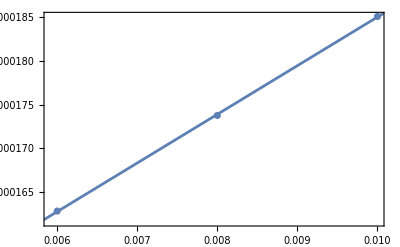

```mathematica
Show[ListPlot[data],Plot[lm[x],{x,0.002,0.012}],Frame->True]
```

```mathematica
NonlinearModelFit[data,10^c*xxx,{c},{xxx}]
```

FittedModel[…]

```mathematica
Log[0.000587]
```

```mathematica
variance={1.65371613165,3.07582913353,5.506185954139999,7.06000961771,9.01275343541,12.764898242800001,24.931752075600002,37.200766994599995,48.322628324600004,58.180580850999995,66.0521152875,86.30203296490001,103.172132904,123.433978374,139.36733619999998,158.63494759,191.667120637,211.86553796700002}*10^(-6)
InputPower={0.0001,0.0002,0.0003,0.0004,0.0005,0.0006,0.001,0.0015,0.002,0.0025,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01}
```

{1.65372×10^-6,3.07583×10^-6,5.50619×10^-6,7.06001×10^-6,9.01275×10^-6,0.0000127649,0.0000249318,0.0000372008,0.0000483226,0.0000581806,0.0000660521,0.000086302,0.000103172,0.000123434,0.000139367,0.000158635,0.000191667,0.000211866}

{0.0001,0.0002,0.0003,0.0004,0.0005,0.0006,0.001,0.0015,0.002,0.0025,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01}

```mathematica
variance={37.200766994599995,48.322628324600004,58.180580850999995,66.0521152875,86.30203296490001,103.172132904,123.433978374,139.36733619999998,158.63494759,191.667120637,211.86553796700002}*10^(-6)
InputPower={0.0015,0.002,0.0025,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01}
```

{0.0000372008,0.0000483226,0.0000581806,0.0000660521,0.000086302,0.000103172,0.000123434,0.000139367,0.000158635,0.000191667,0.000211866}

{0.0015,0.002,0.0025,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01}

```mathematica
data = Transpose[{InputPower,variance}]
```

{{0.0001,1.65372×10^-6},{0.0002,3.07583×10^-6},{0.0003,5.50619×10^-6},{0.0004,7.06001×10^-6},{0.0005,9.01275×10^-6},{0.0006,0.0000127649},{0.001,0.0000249318},{0.0015,0.0000372008},{0.002,0.0000483226},{0.0025,0.0000581806},{0.003,0.0000660521},{0.004,0.000086302},{0.005,0.000103172},{0.006,0.000123434},{0.007,0.000139367},{0.008,0.000158635},{0.009,0.000191667},{0.01,0.000211866}}

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[…]

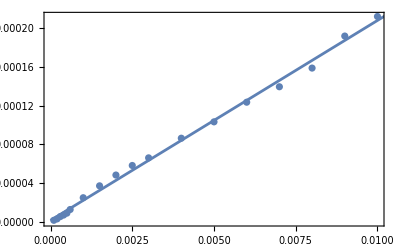

```mathematica
Show[ListPlot[data],Plot[lm[x],{x,0,0.011}],Frame->True]
```